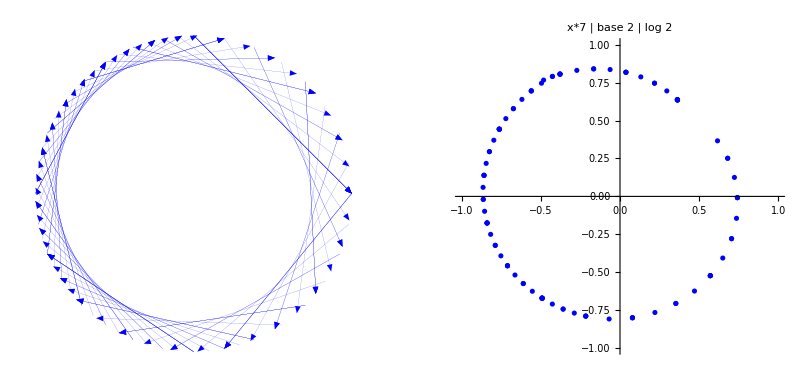

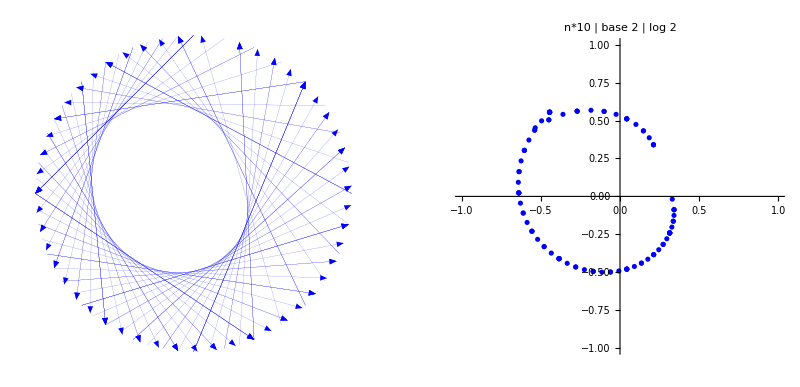

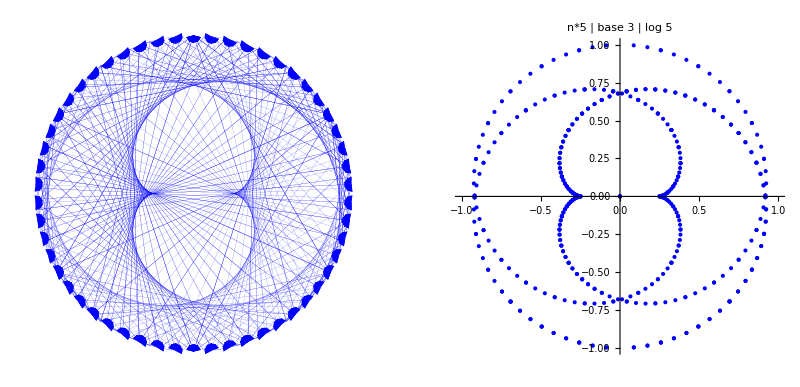

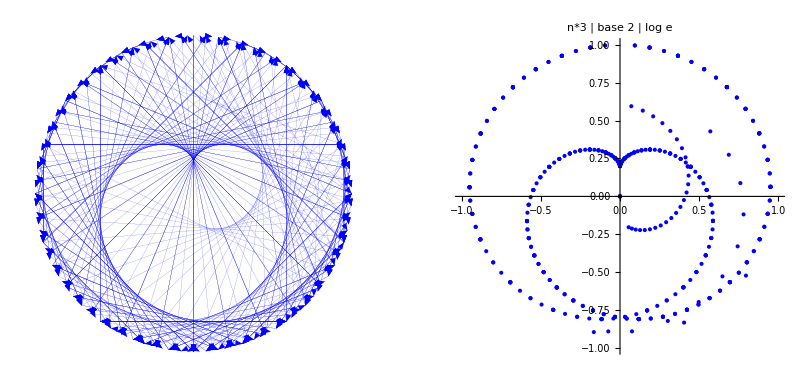

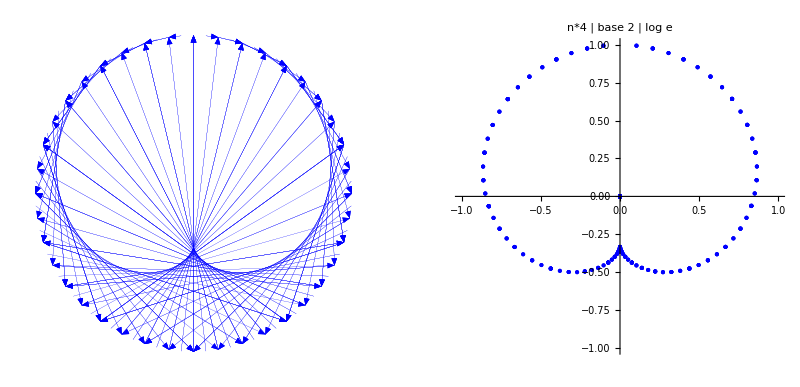

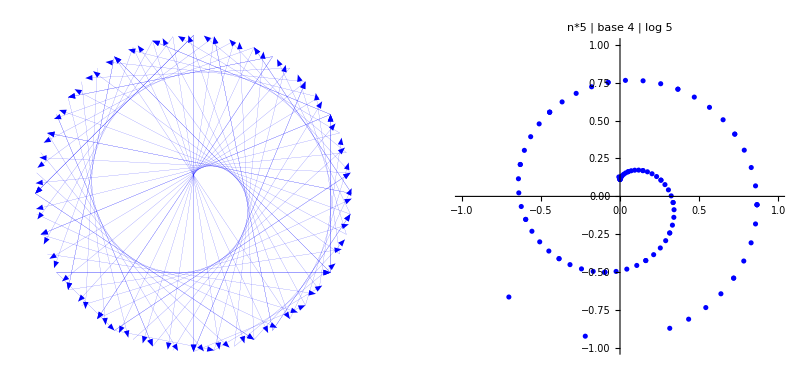

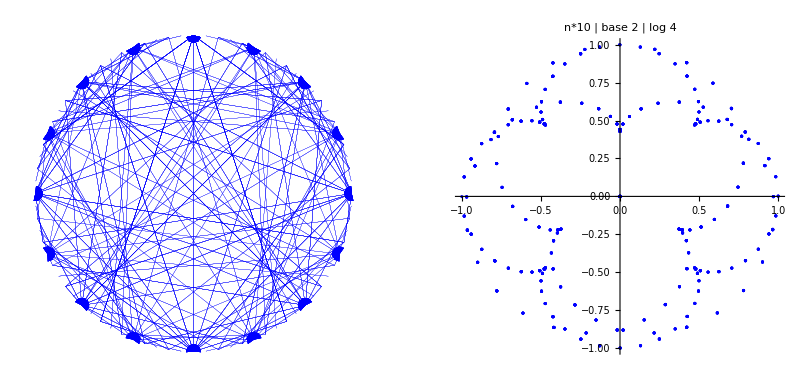

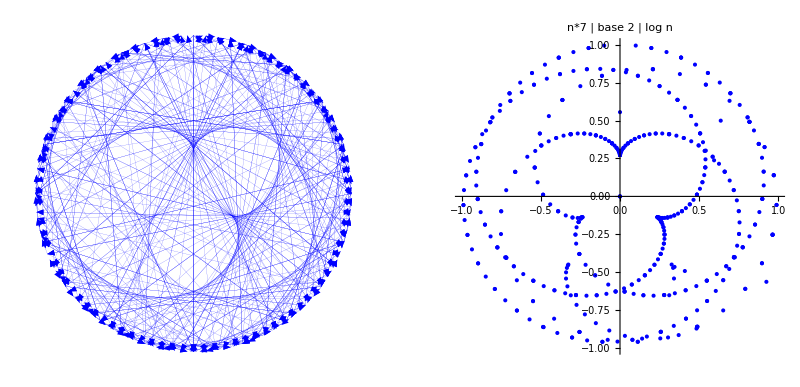

```mathematica
ClearAll["Global`*"];
rotate[t_]:=(x=-Sin[t];y=Cos[t];{x,y});
intersectLines[line1_,line2_]:=(
a11=line1[[1,2]]-line1[[2,2]];a12=line1[[2,1]]-line1[[1,1]];det1=Det[line1];a21=line2[[1,2]]-line2[[2,2]];a22=line2[[2,1]]-line2[[1,1]];det2=Det[line2];detx=Det[{{a12,det1},{a22,det2}}];dety=Det[{{det1,a11},{det2,a21}}];det=Det[{{a11,a12},{a21,a22}}];If[det>0,{detx/det,dety/det},{0,0}]);

generatePlot[f_,g_, step_, label_]:= (
start=1;
stop=100;
e=0.001;
lines1=Table[{rotate[2Pi*g[t]],rotate[2Pi*g[f[t]]]},{t,start,stop,step}];
lines2=Table[{rotate[2Pi*g[t+e]],rotate[2Pi*g[f[t+e]]]},{t,start,stop,step}];
plot1=Graphics[{Blue, Thickness[0.0001],Map[Arrow,lines1],PlotRange->{{-1,1},{-1,1}},AspectRatio->1, PlotLabel->label}];
plot2=ListPlot[MapThread[intersectLines,{lines1,lines2}],PlotRange->{{-1,1},{-1,1}},AspectRatio->1, PlotLabel->label,PlotStyle->Blue];
GraphicsGrid[{{plot1,plot2}}]
);

f[x_]:=x*7;
g[x_]:=x/2^Floor[Log[2,x]];
generatePlot[f, g,1, "x*7 | base 2 | log 2"]

f[n_]:=n*10;
g[n_]:=n/2^Floor[Log[2,n]];
generatePlot[f, g,1, "n*10 | base 2 | log 2"]

f[n_]:=n*5;
g[n_]:=n/(2*3^Floor[Log[5,n]]);
generatePlot[f, g,0.2, "n*5 | base 3 | log 5"]

f[n_]:=n*3;
g[n_]:=n/2^Floor[Log[n]];
generatePlot[f, g,0.2, "n*3 | base 2 | log e"]

f[n_]:=n*4;
g[n_]:=n/2^Floor[Log[n]];
generatePlot[f, g,0.2, "n*4 | base 2 | log e"]

f[n_]:=n*5;
g[n_]:=n/(3*4^Floor[Log[5,n]]);
generatePlot[f, g,1, "n*5 | base 4 | log 5"]

f[n_]:=n*10;
g[n_]:=n/2^Floor[Log[4,n]];
generatePlot[f, g,0.1, "n*10 | base 2 | log 4"]

f[n_]:=n*7;
g[n_]:=n/2^Floor[Log[n]];
generatePlot[f, g,0.2, "n*7 | base 2 | log n"]

f[n_]:=n^3;
g[n_]:=n/2^Floor[Log[2,n]];
generatePlot[f, g,0.3, "n^3 | base 2 | log 2"]

f[n_]:=2^n;
g[n_]:=n/(2*3^Floor[Log[3,n]]);
generatePlot[f, g,0.25, "2^n | base 3 | log 3"]

f[n_]:=2^n;
g[n_]:=n/(5*6^Floor[Log[6,n]]);
generatePlot[f, g,0.25, "2^n | base 3 | log 3"]
```